Import Data

```mathematica
streckeEbene = 27.3;
```

```mathematica
dataPath="../data/2017/Messungen_2017_Geschwindigkeit_Ebene.csv";
dataEbene=SemanticImport@FileNameJoin@{NotebookDirectory[],dataPath}
```

Dataset[<>]

```mathematica
dataEbeneMitGeschw = dataEbene[All,Append[#,"Geschwindigkeit"->streckeEbene /#Zeit]&]
```

Dataset[<>]

## Histogramm

Es wird ein Histogramm erstellt und einer Normalverteilung gegenübergestellt. Für die Kurver der Normalverteilung muss der Erwartungswert und die Standardabweichung berechnet werden.

Berechnung des Mittelwertes und der Standardabweichung

```mathematica
geschwMean = Mean[dataEbeneMitGeschw[All, "Geschwindigkeit"]]
```

1.48076

```mathematica
geschwDeviation = StandardDeviation[dataEbeneMitGeschw[All, "Geschwindigkeit"]]
```

0.144116

Gegenüberstellung von Häufigkeitsverteilung und Normalverteilung. 
ACHTUNG: Das Histogramm wurde mit der Option “PDF” erstellt. Das bedeutet, dass nicht die absoluten Häufigkeiten sondern die Häufigkeitsdichte dargstellt ist, Damit lässt es sich besser mit dem Graphen der Normalverteilung vergleichen. Die Darstellung ist dann nicht mehr von der Anzahl der säulen abhängig.
Bemerkungen wie getrödelt wurden ignoriert. Es wird angenommen, dass im Schnitt es immer Personen gibt, die langsamer oder schneller gehen. Die Probanden hatten keine Vorgabe eine bestimmte Geschwindigkeit einzuhalten. Somit sind auch Probanden zu berücksichtigen, die langsamer gehen. Es ist jedoch anzumerken, dass bei einem Versuch mit nur einer geringen Anzahl von Probanden, solche Sonderheiten eventuell eine signifikante Abweichung verursachen.

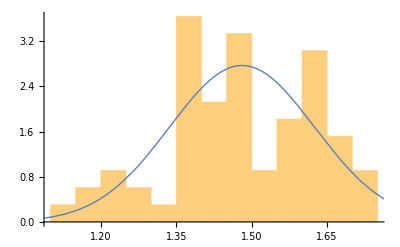

```mathematica
Show[Histogram[dataEbeneMitGeschw[All, "Geschwindigkeit"],10, "PDF"],Plot[PDF[NormalDistribution[geschwMean,geschwDeviation],x],{x,0,2},PlotStyle->Thick]]
```

## Quantileplot

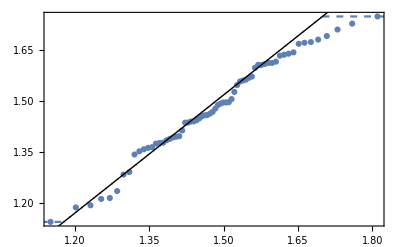

```mathematica
QuantilePlot[dataEbeneMitGeschw[All, "Geschwindigkeit"]]
```

## Distribution Fit Test

```mathematica
DistTestEbene=DistributionFitTest[Array[dataEbeneMitGeschw[All, "Geschwindigkeit"], 66],NormalDistribution[geschwMean,geschwDeviation],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
DistTestEbene["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.426988 | 0.821001
Baringhaus-Henze | 0.269634 | 0.785711
Cramér-von Mises | 0.0560719 | 0.838694
Jarque-Bera ALM | 1.57313 | 0.376383
Mardia Combined | 1.57313 | 0.376383
Mardia Kurtosis | -0.879486 | 0.379138
Mardia Skewness | 0.82605 | 0.363417
Pearson χ^2 | 14.6667 | 0.144695
Shapiro-Wilk | 0.975506 | 0.215767

Der Distribution Fit Test ergibt, dass die Geschwindigkeiten normalverteilt sind. Laut dem Cramer-von Mises Test wird die 5% Hürde überschritten.
Die Geschwindigkeiten auf der Ebene (Wunschgeschwindigkeiten) sind normalverteilt